## Piezo driver noise analysis

Useful references: 
* http://www.ti.com/lit/an/sboa066a/sboa066a.pdf
* http://www.ti.com/lit/an/slva043b/slva043b.pdf

### Preliminaries/Constants

```mathematica
c=299792458;
kB=1.38064852*^-23;
hbar=1.0545718*^-34;
ϵ0=8.85418782*^-12;
a0=.52917721092*^-10;
e=1.602176487*^-19;
pp=1.*^-12;
nn=1.*^-9;
uu=1.*^-6;
mm=1.*^-3;
kk=1.*^3;
MM=1.*^6;
GG=1.*^9;

par[z1_,z2_]:=z1 z2/(z1+z2);
```

### LM7171

The LM7171 is a very high speed, high slew-rate op amp.

```mathematica
OLG:=10.^(85/20); (* open loop gain, = 85dB *)
SR:=4100/uu (*slew rate, V/us*)
Vos:=0.2 mm (* Input offset voltage *)
VosTc:=35uu(*input offset voltage drift, V/degC*)
Ib:=2.7uu (* input bias current *)
Ios:=0.1uu (* input offset current *)
CMRR:=10.^(105/20) (* = 105dB, common mode rejection ratio *)
PSRR:=10.^(90/20) (* = 90dB, power supply rejection ratio *)
en:=14nn (* @10kHz, input-referred voltage noise, V/√Hz *)
in:=1.5pp (* @10kHz, input-referred current noise, A/√Hz *)

VnDAC:=100nn (* @ 1 kHz, conservative @ 10kHz; dac noise *)
```

### Noise analysis

We have the following op amp model:

```mathematica
R1=1MM;
C1=10pp;
R2=20.5kk;
Rmod=1MM;
Cmod=10pp;
Rlp=1kk;
Clp=100nn;


Z1=par[R1,1/(C1 s)];
Z2 = R2;
Zmod = par[Rmod, 1/(Cmod s)];
NG=1+Z1/(par[Z2,Zmod]); (* noise gain *)
Ginv=Z1/par[Z2,Zmod]; (* gain at inverting input node *)
Gmod=Z1/Zmod;
Gdc=(1/(1+Rlp*Clp*s))(1+Z1/(par[Z2, Zmod])) ;(* LP filter * non-inverting gain*)
Zp=par[1/(s Clp),Rlp]; (* impedance seen from non-inverting node *)
Zn=par[par[Z2,Zmod],Z1](* impedance seen at inverting node *)
```

Now, output referred noise for the Op amp is:

Op amp output referred current noise @ 10kHz: 1.36408 uV/√Hz

Op amp output referred voltage noise @ 10kHz: 0.648843 uV/√Hz

Op amp total noise: 1.51053 uV/√Hz

Output-referred Johnson noise @ 10kHz, 300K: 0.846072 uV/√Hz

Output-referred DAC noise @ 10kHz (rough): 2.31729 uV/√Hz

Total output-referred noise @ 10kHz: 2.89265 uV/√Hz = -110.774 dBV/√Hz

Rough RMS noise, 10Hz - 100kHz: 606.716 uVrms

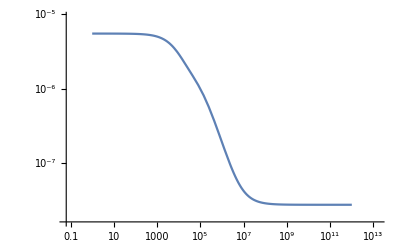

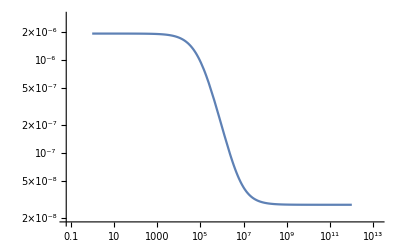

```mathematica
intot=NG √((in*Zp)^2+(in*Zn)^2); (* op amp current noise *)
entot=en NG; (* op amp voltage noise *)
opampNoise=√(intot^2+entot^2) ;(* op amp total intrinsic noise *)

JohnsonNoise=NG(4 kB T (Re[Zn] +Re[Zp] ))^(1/2);(* Johnson noise *)
dacNoise=Gdc VnDAC; (*dac noise *)

totalNoise=√(opampNoise^2+JohnsonNoise^2+dacNoise^2);

Print["Op amp output referred current noise @ 10kHz: ", (intot/.s->10kk)/uu," uV/√Hz"]
Print["Op amp output referred voltage noise @ 10kHz: ", (entot/.s->10kk)/uu," uV/√Hz"]
Print["Op amp total noise: " ,(opampNoise/.s->10kk)/uu, " uV/√Hz"]
Print["Output-referred Johnson noise @ 10kHz, 300K: ", (JohnsonNoise/.{s->10kk,T->300})/uu, " uV/√Hz"]
Print["Output-referred DAC noise @ 10kHz (rough): ", (dacNoise/.s->10kk)/uu," uV/√Hz"]
Print["Total output-referred noise @ 10kHz: ",(totalNoise/.{s->10kk,T->300})/uu, " uV/√Hz = ", 20 Log10[(totalNoise/.{s->10kk,T->300})], " dBV/√Hz"]
nf[s_]:=totalNoise/.T->300//FullSimplify;
rms=√NIntegrate[nf[s]^2,{s,10,10^5}];
Print["Rough RMS noise, 10Hz - 100kHz: ", rms/uu, " uVrms"]
LogLogPlot[Evaluate[totalNoise/.T->300],{s,1,10^12}]
```

```mathematica
intot=√((in*Zp*NG)^2+(in*par[Zn,Z1]*NG)^2)/.s->10kk
```

1.36408×10^-6

```mathematica
JohnsonNoise=(4 kB T(Re[par[par[Z2,Zmod],Z1]] NG+Re[par[Rlp,1/(Clp s)]] NG))^(1/2);
Print["Output-referred Johnson noise @ 10kHz, 300K: ", (JohnsonNoise/.{s->10kk,T->300})/uu, " uV/√Hz"]
```

Output-referred Johnson noise @ 10kHz, 300K: 0.12428 uV/√Hz

```mathematica
JohnsonNoise=(4 kB T(Re[par[Z2,Zmod]] Ginv+Re[Z1]+Re[par[Rlp,1/(Clp s)]] NG))^(1/2);
Print["Output-referred Johnson noise @ 10kHz, 300K: ", (JohnsonNoise/.{s->10kk,T->300})/uu, " uV/√Hz"]
```

Output-referred Johnson noise @ 10kHz, 300K: 0.174663 uV/√Hz

```mathematica
JohnsonNoise=(4 kB T(Re[Z2]Ginv+Re[Zmod] Ginv+Re[Z1](*+Re[par[Rlp,1/(Clp s)]] NG*)))^(1/2);
Print["Output-referred Johnson noise @ 10kHz, 300K: ", (JohnsonNoise/.{s->10kk,T->300})/uu, " uV/√Hz"]
```

Output-referred Johnson noise @ 10kHz, 300K: 0.844657 uV/√Hz

Now, for the DAC nosie (spec’d at 1kHz; will be conservative @ 10kHz):

```mathematica
NG=NG-1;
JohnsonNoise=(4 kB T (R2 NG+Rmod NG+Rlp NG))^(1/2);
Print["Output-referred Johnson noise @ 10kHz, 300K: ", (JohnsonNoise/.{s->10kk,T->300})/uu, " uV/√Hz"]
```

Output-referred Johnson noise @ 10kHz, 300K: 0.86632 uV/√Hz

```mathematica
JohnsonNoise=(4  kB T √((Re[Z2](NG-1))^2+(Re[Zmod] (NG-1))^2+(Re[Z1])^2+(Rlp NG)^2))^(1/2);
Print["Output-referred Johnson noise @ 10kHz, 300K: ", (JohnsonNoise/.{(*s->10kk,*)T->300})/uu, " uV/√Hz"]
```

Output-referred Johnson noise @ 10kHz, 300K: 0.000128716 (1.×10^6 (1+0.0000487805 (20500.+(1.×10^17)/((1.×10^6+(1.×10^11)/s) s)))^2+1. (20500.+(1.×10^17)/((1.×10^6+(1.×10^11)/s) s))^2+1.×10^34 Re[1/((1.×10^6+(1.×10^11)/s) s)]^2+2.37954×10^25 (20500.+(1.×10^17)/((1.×10^6+(1.×10^11)/s) s))^2 Re[1/((1.×10^6+(1.×10^11)/s) s)]^2)^(1/4) uV/√Hz

```mathematica
NG
```

50.7805

```mathematica
DacC/(DacR+DacC)
```

1.×10^-10

```mathematica
20 Log10[6.4*^-7]
```

```mathematica
-123.87640052032225`11
```

```mathematica
(11. 10^-9)^2
```

1.21×10^-16

```mathematica
1/(2Pi 20000 100 10.^-9)
```

79.5775

## Misc

```mathematica
VnResistor:=9.29*^-7(*1kHz*);
VnCur:=1.76*^-6; (*still includes resistor noise; not sure how to turn off.*)
VnV:=1.17*^-6;
VnDAC:=5.22*^-6;
VnTot:=√(-VnResistor^2+VnCur^2+VnDAC^2)
Print["VnTot: ", VnTot];
Print["VnTot from sim: ", 6.4*^-6," at 10Hz, and ", 5.47*^-6,", at 1kHz"]
```

VnTot: 5.42982×10^-6

VnTot from sim: 6.4×10^-6 at 10Hz, and 5.47×10^-6, at 1kHz

```mathematica
Z1=50+1/(CC s);
Z2=1/(1/(1MM)+10pp s);
Zg=20.5kk;
Zfb=Z1+Z2;
```

```mathematica
Zfb//FullSimplify
```

50+1/(1.×10^-6+1.×10^-11 s)+(1.×10^6)/s

```mathematica
Limit[par[Z2,Zg],s->0]
```

20088.2

```mathematica
Limit[Zfb/par[Z2,Zg],s->Infinity]
```

∞

```mathematica
Zfb/par[Z2,Zg]//FullSimplify
```

1.0025+49.7805/s+5.×10^-10 s+(4.87805×10^6)/(100000.+1. s)

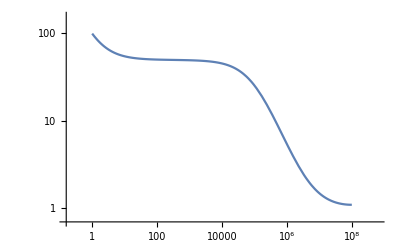

```mathematica
LogLogPlot[1.0024990243902439+49.78048780487805/s+4.999999999999999*^-10 s+(4.878048780487805*^6)/(100000.+1. s),{s,1,100MM}]
```

```mathematica
1.0024990243902439+49.78048780487805/s+4.999999999999999*^-10 s+(4.878048780487805*^6)/(100000.+1. s)/.s->100
```

50.2321

```mathematica
(Zfb/par[Z2,Zg])Z2/(Z1+Z2)//FullSimplify//Expand
```

1.+0.0000487805/(1.×10^-6+1.×10^-11 s)

```mathematica
(Zfb/par[Z2,Zg])Z2/(Z1+Z2)/.s->3
```

49.779

```mathematica
((1+Z2)//FullSimplify//Expand
```

1.+0.0000487805/(1.×10^-6+1.×10^-11 s)

```mathematica
((z1+z2)/par[z2,zg])z2/(z1+z2)
```

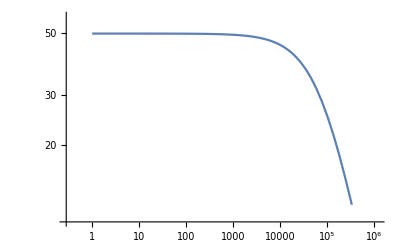

```mathematica
LogLogPlot[Z2/par[Z2,Zg],{s,1,1MM}]
```

```mathematica
600nn
```

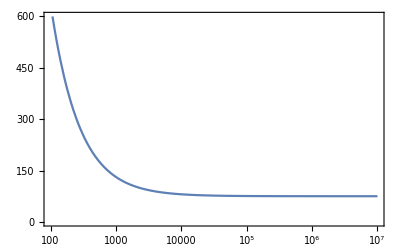

```mathematica
LogLinearPlot[75(1+.75kk/x),{x,100,10MM},PlotRange->{{100,10MM},{0,600}},Frame->True,GridLines->Automatic]
```

```mathematica
LogLogPlot[75(1+.75kk/x),{x,100,10MM},PlotRange->{{100,10MM},{0,600}},Frame->True,GridLines->Automatic]
```

```mathematica
R3=1kk;
R4=1MM;
R2=20.5kk;
R1=1MM;
(*NG=R1/par[R2,R4];*)
NG=1+R1/par[R2,R4];
(*Ginv=R1/par[R2,R1];*)
Ginv=R1/par[R2,R4];
T=300;
√(4kB T NG^2(par[R1,par[R2,R4]]+R3))
```

9.40235×10^-7

```mathematica
√(4kB T (Ginv^2 par[R4,R2]+R1 + NG^2 R3))
```

9.40235×10^-7

```mathematica
√(4kB T (NG^2 par[R1,R2]+NG^2 R3 + Ginv^2 R4))
```

6.47746×10^-6

```mathematica
√(4 kB T(R1+R2 (R1/R2)+R4 Ginv+R3 NG))
```

2.24785×10^-7

```mathematica
√(4 kB T(R3 NG^2+par[R2,R1] NG^2))
```

9.30489×10^-7

```mathematica
√(4 kB T 1kk)NG
```

2.02624×10^-7

```mathematica
√(4 kB T(R2 Ginv^2+R1+R3 NG^2))
```

9.30489×10^-7